```mathematica
Clear[r]
```

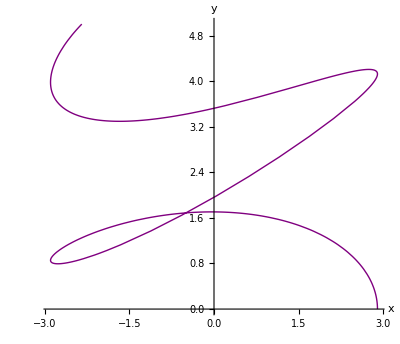

```mathematica
r[t_]={2.9Cos[3.2π*t],(Sin[4π*t]+5t)};
Merp = ParametricPlot[r[t], {t, 0, 1},
AxesLabel->{Style["x",Medium],Style["y",Medium]},PlotStyle->{Thick,Purple}]
```

```mathematica
Speed=D[r[t],t]
Acceleration = D[Speed, t]
```

{-29.154 Sin[10.0531 t],5+4 π Cos[4 π t]}

```mathematica
{-293.0877722947496 Cos[10.053096491487338 t],-16 π^2 Sin[4 π t]}
```

```mathematica
Mer=ArcCurvature[r[t], t]
```

√((53.1222 (3.92699 Cos[10.0531 t]+19.7392 Cos[10.0531 t] Cos[4 π t]+24.805 Cos[10.0531 t] Cos[4 π t]^2+2.84217×10^-14 Cos[10.0531 t] Sin[10.0531 t]^2+12.337 Sin[10.0531 t] Sin[4 π t]+31.0063 Cos[4 π t] Sin[10.0531 t] Sin[4 π t])^2)/(1.5625+7.85398 Cos[4 π t]+π^2 Cos[4 π t]^2+53.1222 Sin[10.0531 t]^2)^4+(2821.96 (0.+3.14159 Cos[10.0531 t] Sin[10.0531 t]+7.89568 Cos[10.0531 t] Cos[4 π t] Sin[10.0531 t]+9.8696 Sin[10.0531 t]^2 Sin[4 π t])^2)/(1.5625+7.85398 Cos[4 π t]+π^2 Cos[4 π t]^2+53.1222 Sin[10.0531 t]^2)^4)

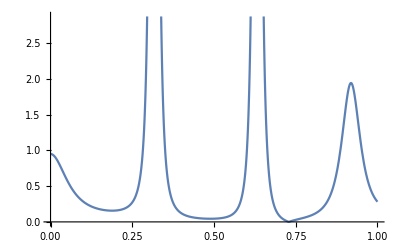

```mathematica
Plot[Mer, {t, 0, 1}]
```

```mathematica
Meh = Norm[Acceleration]
```

√(85900.4 Abs[Cos[10.0531 t]]^2+256 π^4 Abs[Sin[4 π t]]^2)

```mathematica
Plot[Meh, {t, 0, 1}]
```

-Graphics-